## This is the GUI part of the Notebook. The GUI will be contained within this notebook, as well as other functions.

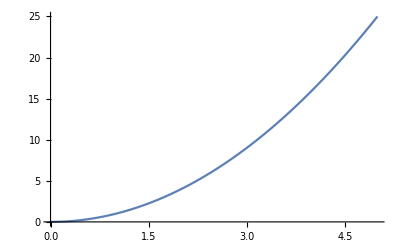

```mathematica
(*This is the part of the function that provides a Graphical User Interface. It is meant to be copied directly into the other notebook and used accordingly. It is defined and tested below.*)

examplefunc[f_]:=Plot[f[x],{x,0,5}];
finalf[x_]=x^2;
examplefunc[finalf]
graphicalUserInterface[diffusion_,listvars_]:=Module[{copyvars=listvars,},
Manipulate[diffusion[listvars],{listvars}];
0
]
```